see more on stackoverflow, the following code was offered  by Chris Degnen.

```mathematica
http://stackoverflow.com/questions/43164238/how-to-build-up-a-backtesting-program-with-mathematica
```

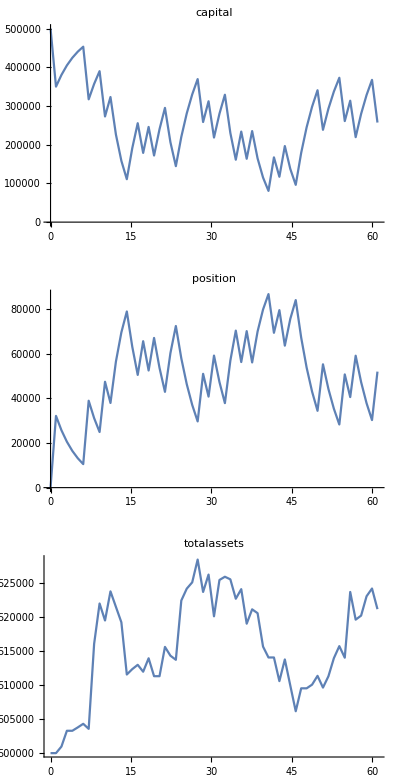

```mathematica
listPrice={{4.66,-0.05},{4.69,0.03},{4.78,0.09},{4.78,0.},{4.81,0.03},{4.85,0.04},{4.78,-0.07},{5.1,0.32},{5.29,0.19},{5.19,-0.1},{5.28,0.09},{5.22,-0.06},{5.18,-0.04},{5.07,-0.11},{5.08,0.01},{5.09,0.01},{5.07,-0.02},{5.1,0.03},{5.05,-0.05},{5.05,0.},{5.13,0.08},{5.1,-0.03},{5.09,-0.01},{5.21,0.12},{5.24,0.03},{5.26,0.02},{5.35,0.09},{5.19,-0.16},{5.24,0.05},{5.09,-0.15},{5.18,0.09},{5.19,0.01},{5.18,-0.01},{5.13,-0.05},{5.15,0.02},{5.06,-0.09},{5.09,0.03},{5.08,-0.01},{5.01,-0.07},{4.99,-0.02},{4.99,0.},{4.94,-0.05},{4.98,0.04},{4.92,-0.06},{4.87,-0.05},{4.91,0.04},{4.91,0.},{4.92,0.01},{4.95,0.03},{4.9,-0.05},{4.93,0.03},{4.99,0.06},{5.04,0.05},{4.98,-0.06},{5.17,0.19},{5.07,-0.1},{5.08,0.01},{5.14,0.06},{5.17,0.03},{5.07,-0.1}};

initCapital=500000;(*min to 0*)initPosition=0;(*max to 100000*)p1=0.3;
p2=0.2;

capital={initCapital};
position={initPosition};
totalassets={initCapital};

buy[p1_,price_]:=Module[{value},value=Last[capital] p1 (*or use p1/100*);
(*check limits*)If[Last[position]+value/price>100000||Last[capital]-value<0,(*skip transaction*)AppendTo[position,Last[position]];
AppendTo[capital,Last[capital]];
AppendTo[totalassets,Last[totalassets]],(*or make transaction*)AppendTo[position,Last[position]+value/price];
AppendTo[capital,Last[capital]-value];
AppendTo[totalassets,price Last[position]+Last[capital]];
{"buy",p1,value,Last[capital]}]]

sell[p2_,price_]:=Module[{quantity},quantity=Last[position] p2 (*or use p2/100*);
(*make transaction*)AppendTo[position,Last[position]-quantity];
AppendTo[capital,Last[capital]+quantity*price];
AppendTo[totalassets,price Last[position]+Last[capital]];
{"sell",p2,quantity*price,Last[capital]}]

backtestDo[list_List]:=If[list[[2]]<0,buy[p1,First[list]],sell[p2,First[list]]]

backtestDo/@listPrice;

GraphicsColumn[Map[ListLinePlot[ToExpression[#],DataRange->Length[listPrice]+1,PlotLabel->#,ImagePadding->{{40,10},{Automatic,Automatic}}]&,{"capital","position","totalassets"}],ImageSize->400]
```